```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["DATA & code definitions :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

DATA & code definitions :

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

XZ uneven noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Depolarizing noise with Measurement error

## 5 qubit planar

```mathematica
{syndromesP5,polyP5}=<<"data/planar5.txt";
```

```mathematica
syndromeDistance[s1_,s2_]:=Count[s1 s2,-1]
syndromeMeasurementProbability[D_,nS_,q_]:=If[q==0,
If[D==0,1,0],((1-q)^(nS-D))q^D]

computePolyMatrixXZ[results_,nQ_,pVal_]:=Module[{polynomials,pxVal,pzVal},
polynomials = polynomialXZ[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
{pxVal,pzVal}=pxpz[1,pVal];
polynomials/.{px->pxVal}
]
computePolyMatrixDepol[results_,nQ_,pVal_]:=Module[{polynomials},
polynomials = polynomialDepol[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
polynomials/.{p->pVal}
]


computeSuccessRate[syndromes_,polynomials_,nQ_,p_,q_]:=Module[{fMatrix,distances,nS,syndromeProbs,j,maxProb,m,nStabs,mTensor},

nStabs=Length[syndromes[[1]]];
nS=Length[syndromes];
(* precompute these, based only on p, so hold for all q *)
fMatrix=computePolyMatrixXZ[polynomials,nQ,p];If[Plus@@Flatten@fMatrix≠1,Print["ERROR: fMatrix doesn't sum to 1"]];
distances=Table[syndromeDistance[syndromes[[i]],syndromes⟦j⟧],{i,1,nS},{j,1,nS}];
(* add layers including q value *)
syndromeProbs=syndromeMeasurementProbability[#,nStabs,q]&/@#&/@distances;
mTensor=Table[(# fMatrix[[j]] &/@ syndromeProbs[[j]]),{j,1,nS}];
Plus@@(Max@#&/@mTensor)

]

computeFMat[syndromes_,polynomials_,nQ_,p_]:=Module[{fMatrix},
fMatrix=computePolyMatrixXZ[polynomials,nQ,p];

If[Plus@@Flatten@fMatrix≠1,Print[{"ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined",Plus@@Flatten@fMatrix}]];
fMatrix
]

syndromeDistances[syndromes_,nS_]:=Table[syndromeDistance[syndromes[[i]],syndromes⟦j⟧],{i,1,nS},{j,1,nS}];
```

```mathematica
computeMEq[fMatrix_,distances_,q_,nS_,nStabs_]:=Module[{syndromeProbs,mTensor},
syndromeProbs=syndromeMeasurementProbability[#,nStabs,q]&/@#&/@distances;
mTensor=Table[(# fMatrix[[j]] &/@ syndromeProbs[[j]]),{j,1,nS}];
Plus@@(Max@#&/@mTensor)
]
computeMEq2[fMatrix_,distances_,q_,nS_,nStabs_]:=Module[{syndromeProbs,mTensor},
syndromeProbs=syndromeMeasurementProbability[#,nStabs,q]&/@#&/@distances;
mTensor=Table[(# fMatrix[[j]] &/@ syndromeProbs[[j]]),{j,1,nS}];
Plus@@(Max@#&/@mTensor)
]

computeMEsuccessRate[syndromes_,polynomials_,nQ_,p_,qRange_,precomputedDistance_:None]:=
Module[{fMatrix,distances,nS,nStabs,fVec},
nStabs=Length[syndromes[[1]]];
nS=Length[syndromes];
fMatrix=computeFMat[syndromes,polynomials,nQ,p];
fVec=Max[#]&/@fMatrix;

distances = syndromeDistances[syndromes,nS];
computeMEq[fMatrix,distances,#,nS,nStabs]&/@qRange
(*computeMEq2[fVec,distances,#,nS,nStabs]&/@qRange*)
]

successRateArray[syndromes_,poly_,nQ_,pRange_,qRange_]:=Module[{qR,pR,test},
pR = Table[p,{p,pRange[[1]],pRange[[2]],pRange[[3]]}];
qR=Table[q,{q,qRange[[1]],qRange[[2]],qRange[[3]]}];

test=Table[computeMEsuccessRate[syndromes,poly,nQ,p,qR],{p,pRange[[1]],pRange[[2]],pRange[[3]]}];

ArrayFlatten[Table[{pR[[i]],qR[[j]],test[[i,j]]},{i,1,Length[pR]},{j,1,Length[qR]}],1]
]


encodingPowerArray[successArray_]:={#[[1]],#[[2]],#[[3]]/(1-#[[1]])}&/@successArray
encodingPowerPQArray[successArray_]:={#[[1]],#[[2]],#[[3]]/((1-#[[2]])(1-#[[1]]))}&/@successArray

correctingPower[p_,q_,pLogical_]:=(1-(1-p)(1-q))/pLogical
correctingPowerArray[successArray_]:={#[[1]],#[[2]],correctingPower[#[[1]],#[[2]],1-#[[3]]]}&/@successArray
```

## Generate data

```mathematica
CellPrint[Cell["DATA :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"data_summary.nb"],Appearance->"DialogBox"]
```

DATA :

### 5 qubit planar

```mathematica
planar5MEdata =successRateArray[syndromesP5,polyP5,5,{0.001,0.2,0.01},{0,0.01,0.001}];
planar5MEdata>>"data/planar5MEdata"
```

### 8 qubit planar

```mathematica
planar8MEdata = successRateArray[syndromesP8,polyP8,8,{0.001,0.12,0.001},{0,0.003,0.003}];
planar8MEdata>>"data/planar8MEdata"
```

### 9 qubit planar

```mathematica
{syndromesP9,polyP9}=<<"data/planar9.txt";
planar9MEdata = successRateArray[syndromesP9,polyP9,9,{0.001,0.17,0.01},{0,0.005,0.0003}];
planar9MEdata>>"data/planar9MEdata"
```

### 7 qubit color code

```mathematica
{syndromesC7,polyC7}=<<"data/color7.txt";
color7MEdata = successRateArray[syndromesC7,polyC7,7,{0.001,0.15,0.005},{0,0.006,0.0005}];
color7MEdata>>"data/color7MEdata"
```

### 11 qubit color code

```mathematica
{syndromesC11,polyC11}=<<"data/color11.txt";
color11MEdata = successRateArray[syndromesC11,truncatePolynomials[polyC11,8],11,{0.001,0.16,0.01},{0,0.004,0.0005}];
color11MEdata>>"data/color11MEdata"
```

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,1.}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,1.}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,1.}

«5 more identical outputs»

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999999}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999998}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999997}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999993}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999988}

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.999978}

### 13 qubit planar

```mathematica
{syndromesP13,polyP13}=<<"data/planar13.txt";
```

```mathematica
planar13MEdata=successRateArray[syndromesP13,truncatePolynomials[polyP13,7],13,{0.001,0.2,0.05},{0,0.005,0.001}];
planar13MEdata>>"data/planar13MEdata"
```

$Aborted

```mathematica
truncPoly13=truncatePolynomials[polyP13,5];
```

```mathematica
Timing[computeMEsuccessRate[syndromesP13,truncPoly13,13,0.1,{0.01}]]
```

4096

{ERROR: fMatrix doesn't sum to 1. Check the number of qubits is correctly defined,0.998275}

fMat calculated

$Aborted

```mathematica
syndromeDistances[syndromes_,nS_]:=Table[syndromeDistance[syndromes[[i]],syndromes⟦j⟧],{i,1,nS},{j,1,nS}];
```

```mathematica
syndromeDistances2[s_,syndromes_]:=syndromeDistance[s,#]&/@syndromes
```

```mathematica
Timing@(syndromeDistances2[#,syndromesP13]&/@syndromesP13)
```

{0.07914,{1}}
 |  |  |  |

```mathematica
Timing@syndromeDistances[syndromesP8,Length[syndromesP8]]
```

{0.08989,{1}}
 |  |  |  |

## Planar code results

```mathematica
planar8MEdata=<<"data/planar8MEdata";
planar9MEdata=<<"data/planar9MEdata";
planar13MEdata=<<"data/planar13MEdata";
color7MEdata = <<"data/color7MEdata";
color11MEdata=<<"data/color11MEdata";
```

### plot functions

```mathematica
epP[data_,color_:1,dashing_:0,thickness_:0.01]:=ListContourPlot[encodingPowerArray[data],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Dashing[dashing],Thickness[thickness],ColorData[97,color]]]
epPQ[data_,color_:1,dashing_:0,thickness_:0.01]:=ListContourPlot[encodingPowerPQArray[data],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Dashing[dashing],Thickness[thickness],ColorData[97,color]]]

cp[data_,color_:1,dashing_:0,thickness_:0.01]:=ListContourPlot[correctingPowerArray[data],PlotRange->{0,2},FrameLabel->{"p","q"},ContourShading->None,Contours->1,ContourStyle->Directive[Opacity[1],Dashing[dashing],Thickness[thickness],ColorData[97,color]]]

cp2[data_]:=ListContourPlot[correctingPowerArray[data],PlotRange->{0.9999,10},FrameLabel->{"p","q"},Contours->Range[10],ColorFunction->ColorData[{"LakeColors","Inverse"}]]

epContour[data_,color_:1,dashing_:0,thickness_:0.01]:=ListContourPlot[encodingPowerPQArray[data],
PlotRange->{1,1.05},
FrameLabel->{"p","q"},
ColorFunction->ColorData[{"LakeColors","Inverse"}],
Contours->{1.000001,1.005,1.01,1.015,1.02,1.025,1.03,1.035}]
```

### 8 qubit planar code

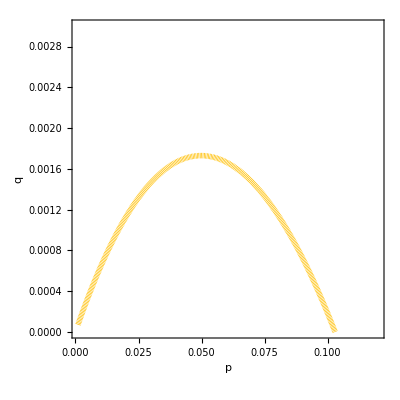
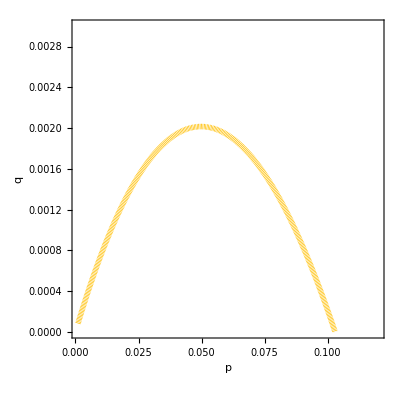
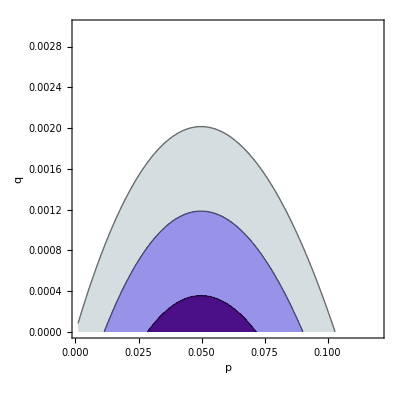
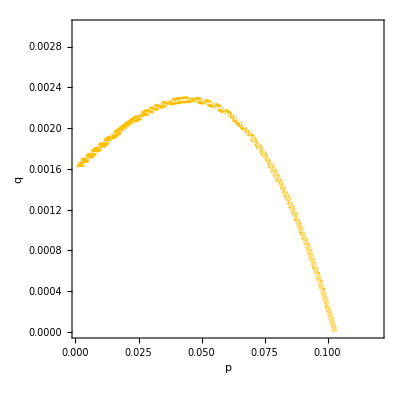
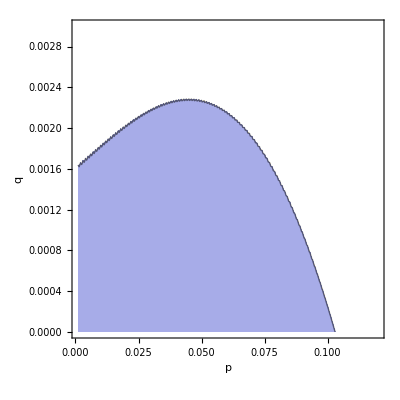

```mathematica
plotsP8={epP[planar8MEdata,8],epPQ[planar8MEdata,8],epContour[planar8MEdata,8],cp[planar8MEdata,8],cp2[planar8MEdata]}
```

### 9 qubit planar code

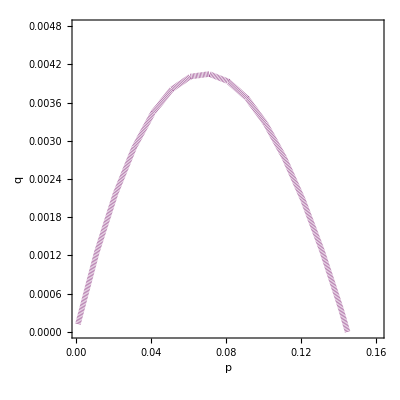
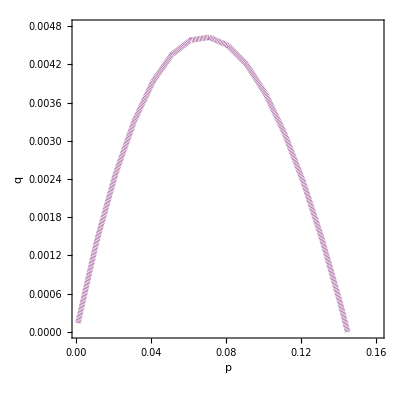
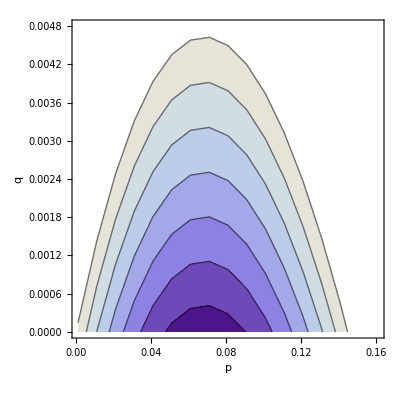
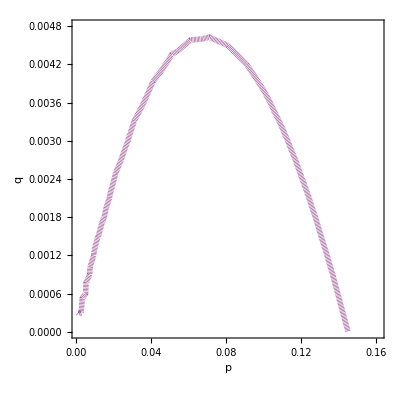

```mathematica
{plotP9ME,plotP9ME2,plotP9ME3,plotP9ME4}={epP[planar9MEdata,9],epPQ[planar9MEdata,9],epContour[planar9MEdata,9],cp[planar9MEdata,9]}
```

### 13 qubit planar code

```mathematica
plotP13ME=ListContourPlot[encodingPowerArray[planar13MEdata],PlotRange->{1,1.05},FrameLabel->{"p","q"}]
```

## Color codes

### 7 qubit color code

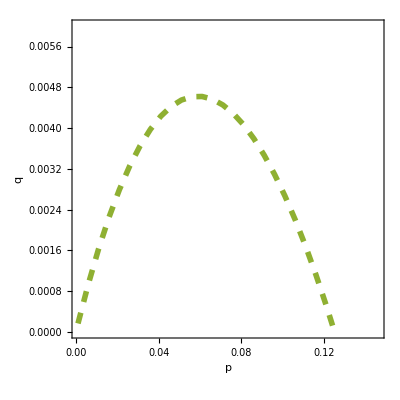
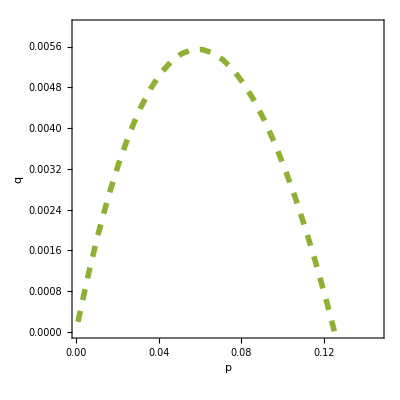
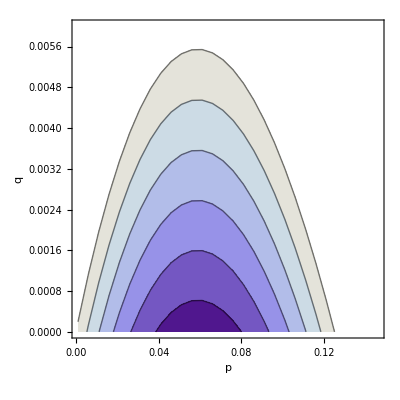
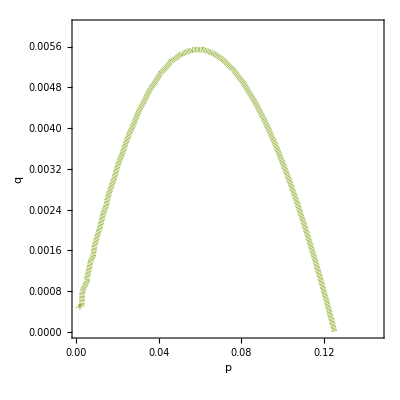

```mathematica
{plotC7ME,plotC7ME2,plotC7ME3,plotC7ME4}={epP[color7MEdata,3,0.02],epPQ[color7MEdata,3,0.02],epContour[color7MEdata,3],cp[color7MEdata,3]}
```

### 11 qubit color code

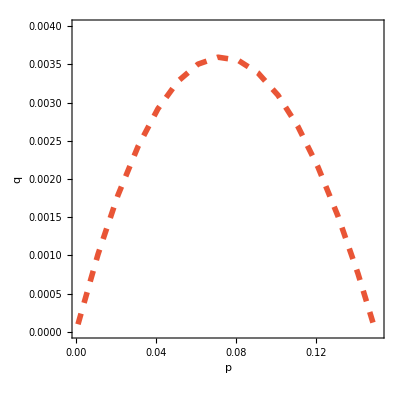
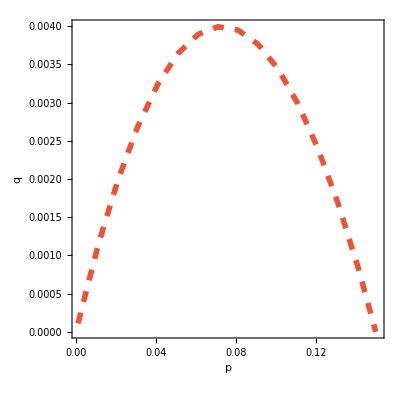
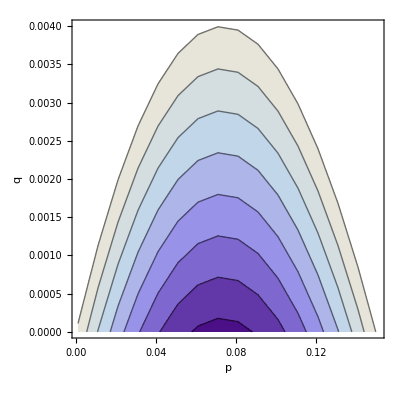

```mathematica
{plotC11ME,plotC11ME2,plotC11ME3}={epP[color11MEdata,11,0.02],epPQ[color11MEdata,11,0.02],epContour[color11MEdata,11]}
```

### gauge color code

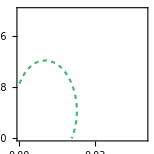

```mathematica
pGCCXZ[p_,a_]:=Module[{px,pz,nx,nz,e1x,e1z},
{px,pz}=pxpz[a,p];
nx=(1-px)^15;
nz=(1-pz)^15;
e1x=15*(1-px)^14*px;
e1z=15*(1-pz)^14*pz;
(nx+e1x)(nz+e1z)
]

qGCC[q_]:=Module[{noError,e1,e2},
noError=(1-q)^18;
e1=18*(1-q)^17*q; (* 1 error in each channel*)
e2=(36+54+3)(1-q)^16*q^2;(* 2 measurement errors on different stabilizers  *)
(noError +e1+e2)^2
]
gcc15data=ArrayFlatten[Table[{p,q,pGCCXZ[p,1]qGCC[q]},{p,0,0.05,0.0002},{q,0,0.02,0.0005}],1];

plotGCCXZ=ContourPlot[pGCCXZ[p,1]qGCC[q]/((1-p)(1-q)),{p,0,0.05},{q,0,0.02},PlotRange->{0.5,1.5},Contours->1,ContourShading->None,ContourStyle->Directive[Opacity[1],Dashing[0.02],Thickness[0.01],ColorData[97,15]]]
```

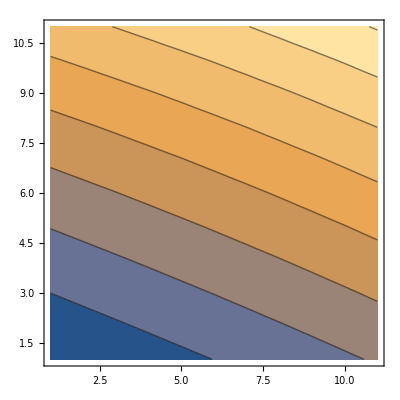

```mathematica
ListContourPlot[Table[(1-(1-p)(1-q))/(pGCCXZ[p,1]qGCC[q]),{p,0,0.05,0.005},{q,0,0.02,0.002}]]
```

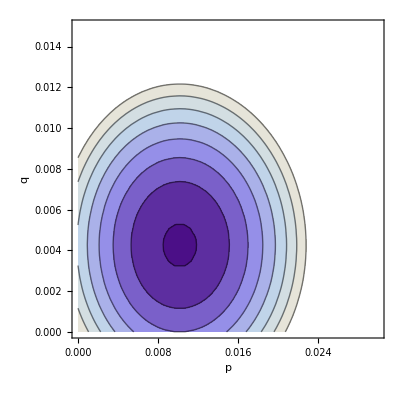

```mathematica
plotGCCXZ3=ContourPlot[pGCCXZ[p,1]qGCC[q]/((1-p)(1-q)),{p,0,0.03},{q,0,0.015},PlotRange->{1,1.05},
FrameLabel->{"p","q"},
ColorFunction->ColorData[{"LakeColors","Inverse"}],
Contours->{1.000001,1.001,1.002,1.003,1.004,1.005,1.006,1.007}]
```

## Summary plot - Correcting power

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

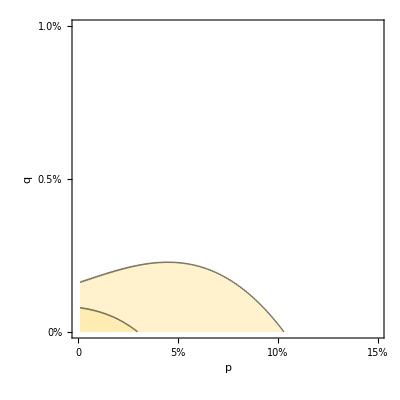
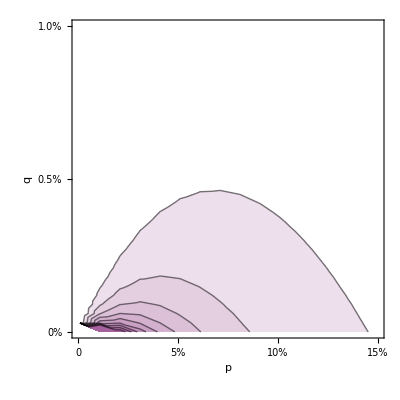
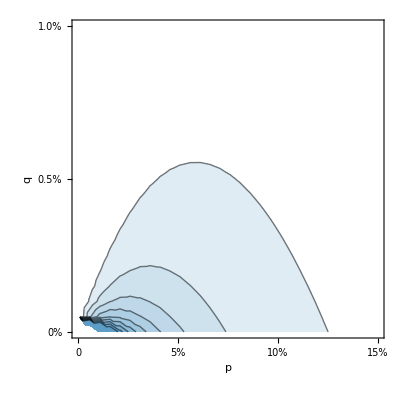
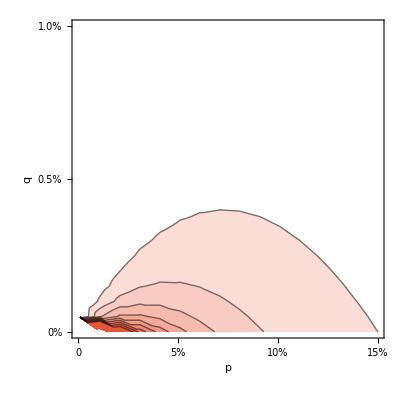
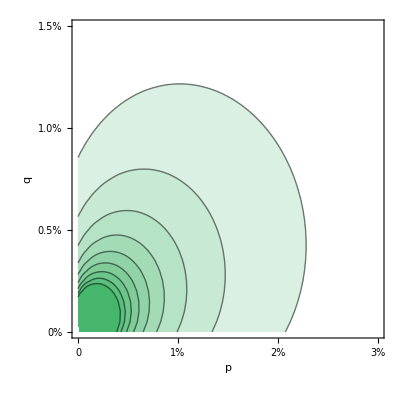

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

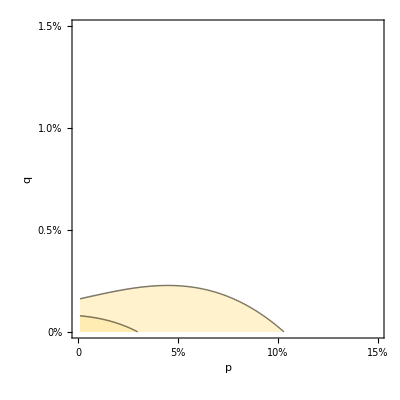
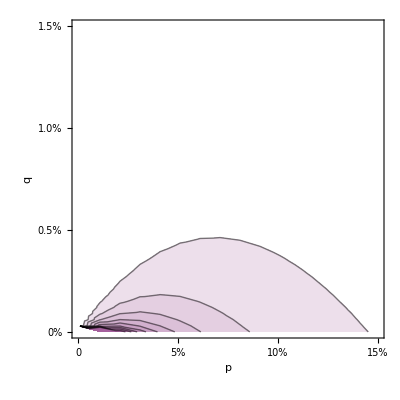
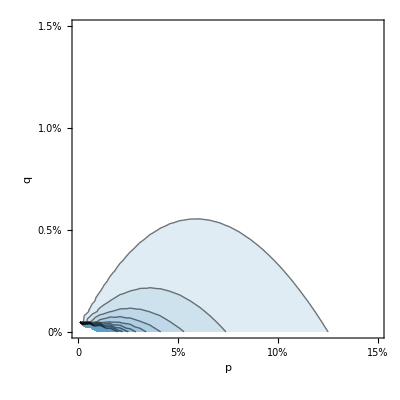
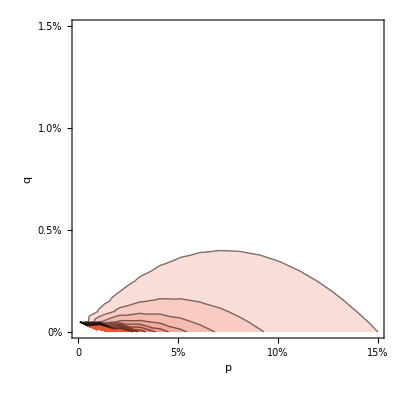
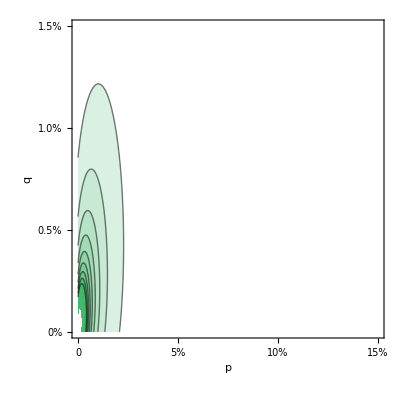

```mathematica
cp1[data_,col_]:=ListContourPlot[correctingPowerArray[data],
PlotRange->{{0,0.15},{0,0.015},{0.9999,10}},
FrameLabel->{"p","q"},
LabelStyle->20,
Contours->Range[10]*0.5,
ContourShading->Table[Blend[{White,ColorData[97,col]},x],{x,0,1,1/10}],FrameTicks->{{0,{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.005,"0.5%"},{0.01,"1.0%"},{0.015,"1.5%"}},{},{}}]

cp2[data_,col_]:=ListContourPlot[correctingPowerArray[data],
PlotRange->{{0,0.15},{0,0.01},{0.9999,10}},
FrameLabel->{"p","q"},
LabelStyle->20,
Contours->Range[10]*0.5,
ContourShading->Table[Blend[{White,ColorData[97,col]},x],{x,0,1,1/10}],FrameTicks->{{0,{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.005,"0.5%"},{0.01,"1.0%"},{0.015,"1.5%"}},{},{}}]

cp3[data_,col_]:=ListContourPlot[correctingPowerArray[data],
PlotRange->{{0,0.03},{0,0.015},{0.9999,100}},
FrameLabel->{"p","q"},
Contours->Range[10]*0.5,
LabelStyle->20,
ContourShading->Table[Blend[{White,ColorData[97,col]},x],{x,0,1,1/10}],FrameTicks->{{0,{0.01,"1%"},{0.02,"2%"},{0.03,"3%"}},{{0,"0%"},{0.005,"0.5%"},{0.01,"1.0%"},{0.015,"1.5%"}},{},{}}]

{cp2[#[[1]],#[[2]]]&/@{{planar8MEdata,8},{planar9MEdata,9},{color7MEdata,7},{color11MEdata,11}},

cp3[gcc15data,15]
}
cp1[#[[1]],#[[2]]]&/@{{planar8MEdata,8},{planar9MEdata,9},{color7MEdata,7},{color11MEdata,11},{gcc15data,15}}
```

## Summary plot p_L/(1-p)(1-q)

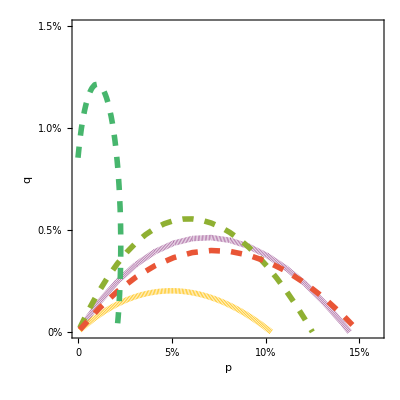

```mathematica
Show[plotP9ME2,plotP8ME2,plotC7ME2,plotC11ME2,plotGCCXZ,PlotRange->{{0,0.16},{0,0.015}},LabelStyle->20,FrameTicks->{{0,{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.005,"0.5%"},{0.01,"1.0%"},{0.015,"1.5%"}},{},{}}]
```

```mathematica
pGCCDepol[p_]:=Module[{noError,e1,x1z1},
noError=(1-p)^15;
e1=15*(1-p)^14*p;
x1z1=15*14*(1-p)^13*(p/3)^2;
noError+e1+x1z1
]
```

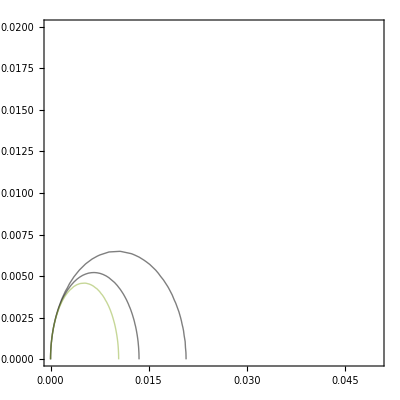

```mathematica
plotGCCDepol=ContourPlot[pGCCDepol[p]qGCC[q]/((1-p)(1-0)),{p,0,0.05},{q,0,0.02},PlotRange->{0.5,1.5},Contours->1,ContourShading->None];
plotGCCXZ=ContourPlot[pGCCXZ[p,1]qGCC[q]/((1-p)(1-0)),{p,0,0.05},{q,0,0.02},PlotRange->{0.5,1.5},Contours->1,ContourShading->None];
plotGCCXZa5=ContourPlot[pGCCXZ[p,100000]qGCC[q]/((1-p)(1-0)),{p,0,0.05},{q,0,0.02},PlotRange->{0.5,1.5},Contours->1,ContourShading->None,ContourStyle->ColorData[97,3]];
Show[plotGCCDepol,plotGCCXZ,plotGCCXZa5]
```